```mathematica
SetDirectory[$HomeDirectory<>"/work/projects/ipsolver"]
```

/Users/mauricio/work/projects/ipsolver

```mathematica
<<SDP`
<<SDPSylvester`
```

### A BAD Ricatti example

Here is data for a more complicated example

```mathematica
n=2;
m=1;

A={{0,1},{1,-1/a}};
B={{0},{1/a}}

Id=IdentityMatrix[n];
Idm=IdentityMatrix[m];

Ze=ConstantArray[0,{n,n}];
Zemm=ConstantArray[0,{m,m}];
Zenm=ConstantArray[0,{n,m}];

IdX=ArrayFlatten[{{Transpose[Zenm]},{Id}}];
IdW=ArrayFlatten[{{Idm},{Zenm}}];
Zenpm=ConstantArray[0,{n+m,n+m}];
```

{{0},{1/a}}

(0 | 1 | 0
1 | -1/a | 1/a
1 | 0 | 0
0 | 1 | 0)_^𝒮

{{0,1/a},{1/a,-1/a^2}}

{(√((1+2 a Conjugate[a]-√(1+4 a Conjugate[a]))/(a^2 Conjugate[a]^2)))/(√2),(√((1+2 a Conjugate[a]+√(1+4 a Conjugate[a]))/(a^2 Conjugate[a]^2)))/(√2)}

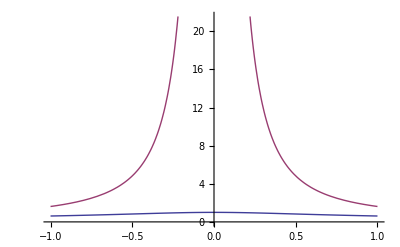

```mathematica
model=StateSpaceModel[{A, B,Id}]
ControllabilityMatrix[model]
SingularValueList[%]
Plot[%,{a,-1,1}]
```

This is the semidefinite program:

min <I,W>
s.t.   A X+B L+X A^T+L^T B^T+I≤0
(X | L^T
L | W)≥0

which we canonical form

```mathematica
aa=1/100000;
aa=1
AA={
{{2 A,Id},{2B,Id},{Zenm,Transpose[Zenm]}},(* A X + B L < -I *)
{{-IdX,Transpose[IdX]},{-2 IdW,Transpose[IdX]},{- IdW,Transpose[IdW]}} (* -[X, L^T; L W] < 0 *)
}/.a->aa
CC={-Id,Zenpm};
BB={Ze,Transpose[Zenm],-Idm};
```

1

{{{{{0,2},{2,-2}},{{1,0},{0,1}}},{{{0},{2}},{{1,0},{0,1}}},{{{0},{0}},{{0,0}}}},{{{{0,0},{-1,0},{0,-1}},{{0,1,0},{0,0,1}}},{{{-2},{0},{0}},{{0,1,0},{0,0,1}}},{{{-1},{0},{0}},{{1,0,0}}}}}

and invoke the solver in the exact same way :

```mathematica
{Y,X,S,iters}=SDPSolve[{AA,BB,CC},SymmetricVariables->{1,3},GapTol->10.^(-13),DebugLevel->0];
```

-------------------------------------------------------------------

Problem data:

* Dimensions (total):

- Variables             = 7

- Inequalities          = 2

* Dimensions (detail):

- Variables             = {{2,2},{1,2},{1,1}}

- Inequalities          = {2,3}

Method:

* Method                  = PredictorCorrector

* Search direction        = NT

Precision:

* Gap tolerance           = 1.e-13

* Rationalize iterates    = False

Other options:

* Debug level             = 0

K    <B, Y>           mu    theta/tau        alpha       |X S|2      |X S|oo   ~|A X - B|  ~|A* X - C|

-----------------------------------------------------------------------------------------------------------

1  1.2940 E  0  1.1468 E -1  2.7800 E -1  9.0369 E -1  1.5549 E  0  9.9528 E -1  2.8109 E-15  2.8978 E-16

2  3.5451 E  0  2.1790 E -2  8.9055 E -2  8.1000 E -1  1.7639 E  0  9.9034 E -1  5.0078 E-13  2.9894 E-16

3  4.3688 E  0  2.8841 E -3  1.1697 E -2  8.6764 E -1  1.6488 E  0  9.8717 E -1  6.9950 E-13  2.6622 E-16

4  4.4601 E  0  2.8856 E -4  1.1445 E -3  9.0000 E -1  1.9615 E  0  9.6110 E -1  5.7760 E-13  1.9230 E-16

5  4.4709 E  0  2.8971 E -5  1.1503 E -4  8.9960 E -1  1.9429 E  0  9.5150 E -1  5.1005 E-12  3.3307 E-16

6  4.4720 E  0  2.9139 E -6  1.1566 E -5  8.9942 E -1  1.9407 E  0  9.5037 E -1  2.5391 E-11  2.3551 E-16

7  4.4721 E  0  2.9341 E -7  1.1639 E -6  8.9931 E -1  1.9403 E  0  9.5007 E -1  1.0532 E-10  3.2368 E-16

8  4.4721 E  0  2.9622 E -8  1.1757 E -7  8.9904 E -1  1.9410 E  0  9.4947 E -1  2.1249 E -9  4.2276 E-16

9  4.4721 E  0  2.9348 E -9  8.1672 E -9  9.0000 E -1  1.9163 E  0  9.9470 E -1  3.2591 E -8  4.7103 E-16

10  4.4721 E  0  2.9063 E -9  8.3106 E -9  8.7280 E -3  1.9206 E  0  9.9957 E -1  2.8470 E -8  3.1402 E-16

11  4.4721 E  0  3.1675 E-10  4.1545 E -9  9.0000 E -1  1.9812 E  0  8.4087 E -1  7.1884 E -8  4.0413 E-16

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1., 1., 1., 1., 1., 0.397161}, {1., 1., « 3 », 0.397162}, « 1 », « 1 », {« 19 », « 4 », « 20 »}, {0.397161, 0.397162, 0.397164, 0.39716, 0.397161, 1.}} may contain significant numerical errors.

WARNING: Unproductive iteration!

Interrupting algorithm.

----------------------------------------------------------------------------------------------

* Primal solution is feasible

(max eig(A* X - C) = -5.37666×10^-9 <= 0 )

* Dual solution is not within tolerance

(|| A X - B || = 2.97778×10^-7 >= 1.×10^-13)

The solution produces a stabilizaing control gain

```mathematica
{X,L,W}=Y;
```

```mathematica
K=L.Inverse[X];
Acl=A+B.K/.a->aa;
Max[Re[Eigenvalues[Acl]]]
```

-0.618033

```mathematica
Max[Eigenvalues[Acl.X+X.Transpose[Acl]+Id]]
```

-8.64659×10^-9

```mathematica
Max[Eigenvalues[W-K.X.Transpose[K]]]
```

3.50986×10^-8